y-y^2/2+y^3/3-y^4/4+y^5/5-y^6/6+y^7/7-y^8/8+y^9/9-y^10/10

Abs[y-y^2/2+y^3/3-y^4/4+y^5/5-y^6/6+y^7/7-y^8/8+y^9/9-y^10/10-Log[1+y]]

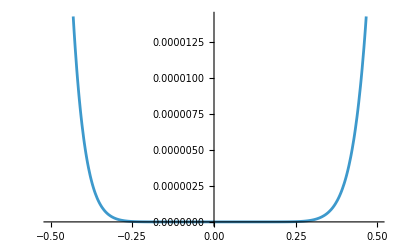

```mathematica
ClearAll["Global`*"];
prim10[y_] = Normal[Series[Log[1 + t], {t, 0, 10}]] /. t-> y
error[y_] = Abs[prim10[y] - Log[y + 1]]
Plot[error[y], {y, -0.5, 0.5}, PlotRange->Automatic]
```

Picewise[{{p10[-1+x],0.5≤x≤1.5},{0,-∞<x<0.5},{0,1.5<x<∞}}]

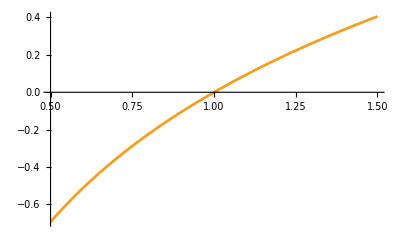

```mathematica
LogLocal[x_] = Picewise[{{p10[x-1], 0.5 <= x <= 1.5}, {0, -Infinity < x < 0.5}, {0, 1.5 < x < Infinity}}]
Plot[{LogLocal[x], Log[x]}, {x, 0.5, 1.5}]
```